```mathematica
(* Newton's Method *)

Nmax = 500;
tol = 10^(-16);
```

```mathematica
newterr[f_,x0_,sol_] :=Module[{xn=x0,xn1,fp,err={}},
fp = D[f,x];
Do[xn1 = N[xn - (f/fp)/. x -> xn];
err = Append[err,xn1];
If[Abs[xn1-sol]<tol,Return[Drop[err,-1]]];
xn = xn1,{i,1,Nmax}];{Drop[Abs[err-xn1],-1]}];
```

```mathematica
newt[f_,x0_] :=Module[{xn=x0,xn1,fp,err={}},
fp = D[f,x];
Do[xn1 = N[xn - (f/fp)/. x -> xn];
err = Append[err,xn1];
If[Abs[xn1-xn]<tol,Return[xn]];
xn = xn1,{i,1,Nmax}];{xn}];
```

```mathematica
(* newt inputs a function and a "guess" for where our root is near and outputs our root, newterr inputs our functionreturns the error at each step*)
```

```mathematica
(* Some Simple Functions *)
```

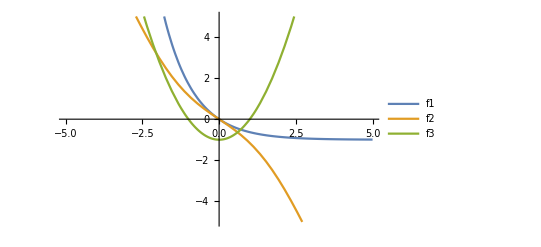

```mathematica
f1[x_]=Exp[-x]-1;
f2[x_] = Sin[x]-2x;
f3[x_] := (x^2) -1;
Plot[{f1[x],f2[x],f3[x]},{x,-5,5},PlotRange->{-5,5},PlotLegends->{"f1","f2","f3"}]
```

```mathematica
newt[f1[x],1]
```

{3.09269×10^-17}

```mathematica
Chop[%]
```

{0}

```mathematica
(* Root for f1 is 0*)
```

```mathematica
(* Now that we know the true root, we can calculate the error at each step. Append is making the lists equal length for a clean looking graph*)
```

```mathematica
err1 = newterr[f1[x],1,0];
err2 = newterr[f2[x],1,0];
err3 = newterr[f3[x],2,1];
err3 = Append[err3[[1]],0];
err2 = Append[err2[[1]],0];
For[i=0,i<3,i++,
err2 = Append[err2,0]]
```

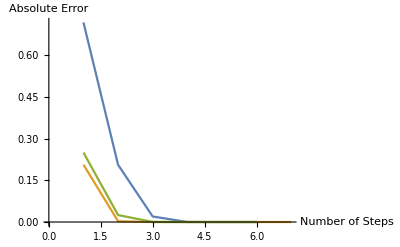

```mathematica
ListLinePlot[{err1[[1]],err2,err3},AxesLabel->{"Number of Steps","Absolute Error"}]
```

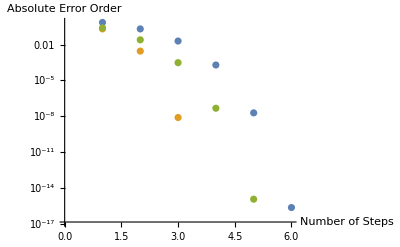

```mathematica
ListLogPlot[{err1[[1]],err2,err3},AxesLabel->{"Number of Steps","Absolute Error Order"}]
```

```mathematica
(* Intuitively, we know that our error should decrease at each step size, unless our initial guess is too far away, which will never be the case with this function. For each function, our guess was only 1 away from our true root, so finding the true root took only a few steps. *)
```

```mathematica
(* A More Complicated Function*)
```

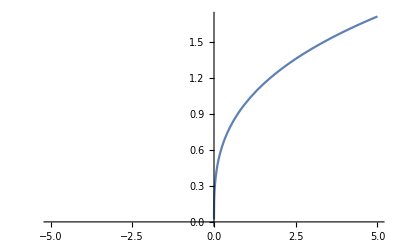

```mathematica
f5[x_] = x^(1/3);
Plot[f5[x],{x,-5,5}]
```

```mathematica
newt[f5[x],0.1]
```

{3.27339×10^149}

```mathematica
(* Even with an incredibly close guess, Newton's method will never find the 0 of the cube root of x. This is because the cube root of x's derivative is undefined at x=0. To calculate this we need a different method.*)
```

```mathematica
(* Bisection Method *)

bisect[f_,a_,b_] := Module[{c,l,r},
l=a;
r=b;
Do[c = N[(l+r)/2];
If[(f/.x -> c) ==0 ,Return[c]];
If[Abs[c]<tol,Return[c]];
If[Sign[(f/.x -> c)] == Sign[(f/.x -> l)],l=c,r=c],{i,1,Nmax}];c];


bisecterr[f_,a_,b_,solu_] := Module[{c,err={},l,r},
l=a;
r=b;
Do[c = N[(l+r)/2];
err = Append[err,c];
If[(f/.x -> c) ==0 ,Return[Abs[err-solu]]];
If[Abs[c]<tol,Return[Abs[err-solu]]];
If[Sign[(f/.x -> c)] == Sign[(f/.x -> l)],l=c,r=c],{i,1,Nmax}];Abs[err-solu]];
```

```mathematica
(* As with the Newton's implementation, we split into two methods, one for finding the root, and one for error analysis. In the Bisection Method, we need two integers that surround our root, so those and our function are our inputs for bisect. These plus our true root are our inputs for bisecterr *)
```

```mathematica
bisect[f5[x],0,2]
```

5.55112×10^-17

```mathematica
Chop[%]
```

0

```mathematica
(* We can thus calculate what Newton's method could not, x=0 for f= x^ (1/3)*)
```

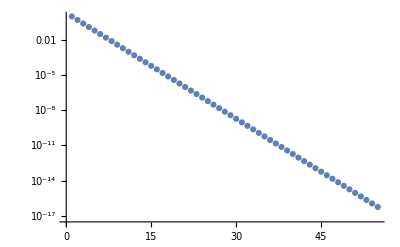

```mathematica
ListLogPlot[bisecterr[f5[x],0,2,0]]
```

```mathematica
(* For a function that has roots that can be found via Newton's method, which is more efficient? *)
(* Revisiting f1: f= e^-x -1*)
```

```mathematica
Manipulate[ListLogPlot[{bisecterr[f1[x],l,r,0],newterr[f1[x],g,0][[1]]},PlotLegends->{"Bisection","Newton's"}],{l,-10,0},{r,0,10},{g,-20,5}]
```

```mathematica
(* Answer: It depends. For most cases, Newton's method will be more efficient than Bisection. However if our initial guess for Newton's method is not near the root, Bisection becomes more efficient. As such, the main drawback of Newton's method is you must know the area where the root is. *)
```